## Anharmonic Oscillator (The units are chosen such that [V]=[Energy])

### Initializing

```mathematica
(*Initializing*)
dx=0.01;xmin=-3;xmax=3;xL=Range[xmin,xmax,dx];Lx=Length[xL];
Vm=xL^4;
```

### Calculations

```mathematica
(*We construct the Hamiltonian matrix from the discritized time independent schrodinger equation such that each row times the column vector of ψ retrives this compnent of the discritized equation (H[[i,j]]ψ[[j]]=-1/2(d^2 ψ)/dx^2+V(x)ψ->-1/2(ψ[[i+1]]-2ψ[[i]]+ψ[[i-1]])/(Δx)^2, j>=1) as you can confirm.*)
(*Initializing first and last rows of H by hand from the equation above, hbar=m=1*)
Hm=Table[0*xL,{i,1,Lx}];Hm[[1,1]]=Vm[[1]]+1/(dx)^2;Hm[[1,2]]=-1/(2(dx)^2);Hm[[-1,-1]]=Vm[[-1]]+1/(dx)^2;Hm[[-1,-2]]=-1/(2(dx)^2);
(*From the analysis pattern we detect that these are the elements of the remaining rows.*)
Do[Hm[[i,i]]=Vm[[i]]+1/(dx)^2;Hm[[i,i-1]]=-1/(2(dx)^2);Hm[[i,i+1]]=-1/(2(dx)^2),{i,2,Lx-1}]
```

### Extracting results and Plotting

Ground State Energy (Matrix): 0.667977

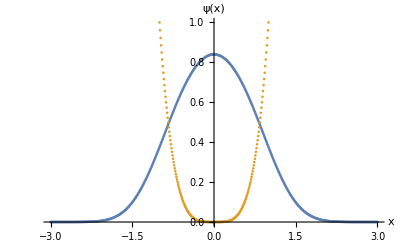

```mathematica
(*Getting the ground state energy and ground state wavefunction which is the last one here, 
since the outcome is arranged from the highest to the lowest.*)
Print["Ground State Energy (Matrix): ",Eigenvalues[Hm][[-1]]]
ψ0=Chop[Eigenvectors[Hm][[-1]]];
ψ=ψ0/Sqrt[dx*(ψ0.ψ0)];(*Already Normalized, but making sure*)

(*Getting ready to plot*)
potential=Table[{xL[[i]],Vm[[i]]},{i,Lx}];
pairs=Table[{xL[[i]],ψ[[i]]},{i,Lx}];
ListPlot[{pairs,potential},AxesLabel->{"x","ψ(x)"},PlotRange->{All,{0,1}}](*In agreement with what we got using the variational method.*)
```